## Formulação das equações dinâmicas

```mathematica
Subscript[z, te][t_] = Z[t] - Subscript[d, 2] Sin[ϕ[t]]Cos[Subscript[α, 2] + ϕ[t]] + Subscript[d, 4] Subscript[θ, e][t];
Subscript[z, td][t_] = Z[t] + Subscript[d, 2] Sin[ϕ[t]]Cos[Subscript[α, 2] - ϕ[t]] + Subscript[d, 4] Subscript[θ, d][t];
Subscript[ΔL, e][t_] = (√(Subscript[d, 1]^2 + Subscript[d, 3]^2 - 2 Subscript[d, 1] Subscript[d, 3] Cos[Subscript[α, 1]]) - √(Subscript[d, 1]^2 + Subscript[d, 3]^2 - 2 Subscript[d, 1] Subscript[d, 3] Cos[Subscript[α, 1] - Subscript[θ, e][t]]))Subscript[d, 7]/Subscript[d, 6];
Subscript[ΔL, d][t_] = (√(Subscript[d, 1]^2 + Subscript[d, 3]^2 - 2 Subscript[d, 1] Subscript[d, 3] Cos[Subscript[α, 1]]) - √(Subscript[d, 1]^2 + Subscript[d, 3]^2 - 2 Subscript[d, 1] Subscript[d, 3] Cos[Subscript[α, 1] - Subscript[θ, d][t]]))Subscript[d, 7]/Subscript[d, 6];
(*Subscript[Z, e][t_] = 180Sin[(2Pi)/f t];
Subscript[Z, d][t_] = 180Sin[(2Pi)/f t + φ];*)
𝒯 = 1/2 Subscript[J, x] ϕ'[t]^2 + 1/2 Subscript[m, s] Z'[t]^2 + 1/2 mt (Subscript[z, te]'[t])^2 + 1/2 mt (Subscript[z, td]'[t])^2;
𝒱 = 1/2 Subscript[k, a](Subscript[ΔL, e][t])^2 + 1/2 Subscript[k, a](Subscript[ΔL, d][t])^2 + 1/2 Subscript[k, t](Subscript[z, te][t] - Subscript[Z, e][t])^2 + 1/2 Subscript[k, t](Subscript[z, td][t] - Subscript[Z, d][t])^2;
ℛ = 1/2 Subscript[c, a](Subscript[ΔL, e]'[t])^2 + 1/2 Subscript[c, a](Subscript[ΔL, d]'[t])^2;
Grid[{
  {"𝒯:", 𝒯//TableForm}
}]
Grid[{
  {"𝒱:", 𝒱//TableForm}
}]
Grid[{
  {"ℛ:", ℛ//TableForm}
}]
```

𝒯: | 1/2 m_s Z'[t]^2+1/2 J_x ϕ'[t]^2+1/2 mt (Z'[t]+Cos[α_2-ϕ[t]] Cos[ϕ[t]] d_2 ϕ'[t]+Sin[α_2-ϕ[t]] Sin[ϕ[t]] d_2 ϕ'[t]+d_4 θ_d'[t])^2+1/2 mt (Z'[t]-Cos[ϕ[t]] Cos[α_2+ϕ[t]] d_2 ϕ'[t]+Sin[ϕ[t]] Sin[α_2+ϕ[t]] d_2 ϕ'[t]+d_4 θ_e'[t])^2

𝒱: | ((√(d_1^2-2 Cos[α_1] d_1 d_3+d_3^2)-√(d_1^2-2 Cos[α_1-θ_d[t]] d_1 d_3+d_3^2))^2 d_7^2 k_a)/(2 d_6^2)+((√(d_1^2-2 Cos[α_1] d_1 d_3+d_3^2)-√(d_1^2-2 Cos[α_1-θ_e[t]] d_1 d_3+d_3^2))^2 d_7^2 k_a)/(2 d_6^2)+1/2 k_t (Cos[α_2-ϕ[t]] Sin[ϕ[t]] d_2+Z[t]-Z_d[t]+d_4 θ_d[t])^2+1/2 k_t (-Cos[α_2+ϕ[t]] Sin[ϕ[t]] d_2+Z[t]-Z_e[t]+d_4 θ_e[t])^2

ℛ: | (Sin[α_1-θ_d[t]]^2 c_a d_1^2 d_3^2 d_7^2 θ_d'[t]^2)/(2 (d_1^2-2 Cos[α_1-θ_d[t]] d_1 d_3+d_3^2) d_6^2)+(Sin[α_1-θ_e[t]]^2 c_a d_1^2 d_3^2 d_7^2 θ_e'[t]^2)/(2 (d_1^2-2 Cos[α_1-θ_e[t]] d_1 d_3+d_3^2) d_6^2)

```mathematica
𝕢[t_] = {ϕ[t], Z[t], Subscript[θ, e][t], Subscript[θ, d][t]};
ℚ[t_] = {0, 0, 0, 0};
EoM = Collect[D[D[𝒯, {𝕢'[t]}],t] - D[D[𝒱, {𝕢'[t]}],t] - D[𝒯, {𝕢[t]}] + D[𝒱, {𝕢[t]}] + D[ℛ, {𝕢'[t]}] - ℚ[t], Join[𝕢''[t], 𝕢'[t]], FullSimplify];
Grid[{
  {":", EoM[[1]]}
}]
Grid[{
  {":", EoM[[2]]}
}]
Grid[{
  {":", EoM[[3]]}
}]
Grid[{
  {":", EoM[[4]]}
}]
```

: | d_2 k_t (Cos[α_2-2 ϕ[t]] (Cos[α_2-ϕ[t]] Sin[ϕ[t]] d_2+Z[t]-Z_d[t]+d_4 θ_d[t])+Cos[α_2+2 ϕ[t]] (Cos[α_2+ϕ[t]] Sin[ϕ[t]] d_2-Z[t]+Z_e[t]-d_4 θ_e[t]))-2 mt Cos[2 α_2] Sin[4 ϕ[t]] d_2^2 ϕ'[t]^2+2 mt Sin[α_2] Sin[2 ϕ[t]] d_2 Z''[t]+((mt+mt Cos[2 α_2] Cos[4 ϕ[t]]) d_2^2+J_x) ϕ''[t]+mt Cos[α_2-2 ϕ[t]] d_2 d_4 θ_d''[t]-mt Cos[α_2+2 ϕ[t]] d_2 d_4 θ_e''[t]

: | k_t (2 Sin[α_2] Sin[ϕ[t]]^2 d_2+2 Z[t]-Z_d[t]-Z_e[t]+d_4 (θ_d[t]+θ_e[t]))+4 mt Cos[2 ϕ[t]] Sin[α_2] d_2 ϕ'[t]^2+(2 mt+m_s) Z''[t]+2 mt Sin[α_2] Sin[2 ϕ[t]] d_2 ϕ''[t]+mt d_4 θ_d''[t]+mt d_4 θ_e''[t]

: | (Sin[α_1-θ_e[t]] d_1 d_3 (-1+(√(d_1^2-2 Cos[α_1] d_1 d_3+d_3^2))/(√(d_1^2-2 Cos[α_1-θ_e[t]] d_1 d_3+d_3^2))) d_7^2 k_a)/d_6^2+d_4 k_t (-Cos[α_2+ϕ[t]] Sin[ϕ[t]] d_2+Z[t]-Z_e[t]+d_4 θ_e[t])+2 mt Sin[α_2+2 ϕ[t]] d_2 d_4 ϕ'[t]^2+(Sin[α_1-θ_e[t]]^2 c_a d_1^2 d_3^2 d_7^2 θ_e'[t])/((d_1^2-2 Cos[α_1-θ_e[t]] d_1 d_3+d_3^2) d_6^2)+mt d_4 Z''[t]-mt Cos[α_2+2 ϕ[t]] d_2 d_4 ϕ''[t]+mt d_4^2 θ_e''[t]

: | (Sin[α_1-θ_d[t]] d_1 d_3 (-1+(√(d_1^2-2 Cos[α_1] d_1 d_3+d_3^2))/(√(d_1^2-2 Cos[α_1-θ_d[t]] d_1 d_3+d_3^2))) d_7^2 k_a)/d_6^2+d_4 k_t (Cos[α_2-ϕ[t]] Sin[ϕ[t]] d_2+Z[t]-Z_d[t]+d_4 θ_d[t])+2 mt Sin[α_2-2 ϕ[t]] d_2 d_4 ϕ'[t]^2+(Sin[α_1-θ_d[t]]^2 c_a d_1^2 d_3^2 d_7^2 θ_d'[t])/((d_1^2-2 Cos[α_1-θ_d[t]] d_1 d_3+d_3^2) d_6^2)+mt d_4 Z''[t]+mt Cos[α_2-2 ϕ[t]] d_2 d_4 ϕ''[t]+mt d_4^2 θ_d''[t]

## Identificação dos pontos de equilíbrio

```mathematica
𝕕[t_] = Join[#, D[#,t], D[#,{t,1}]]& @({ϕ[t] -> 0, Z[t] -> 0, Subscript[θ, e][t] -> 0, Subscript[θ, d][t] -> 0, Subscript[Z, e][t] -> 0, Subscript[Z, d][t] -> 0});
Grid[{
  {"Pontos de equilíbrio:", 𝕕[t]//TableForm}
}]
```

Pontos de equilíbrio: | ϕ[t]→0
Z[t]→0
θ_e[t]→0
θ_d[t]→0
Z_e[t]→0
Z_d[t]→0
ϕ'[t]→0
Z'[t]→0
θ_e'[t]→0
θ_d'[t]→0
Z_e'[t]→0
Z_d'[t]→0
ϕ'[t]→0
Z'[t]→0
θ_e'[t]→0
θ_d'[t]→0
Z_e'[t]→0
Z_d'[t]→0

```mathematica
𝔻[t_] = Join[Solve[Thread[(EoM/.𝕕[t]) == 0], {ϕ''[t], Z''[t], Subscript[θ, e]''[t], Subscript[θ, d]''[t]}]//Flatten//FullSimplify, {Subscript[Z, e]''[t] -> 0, Subscript[Z, d]''[t] -> 0}];
Grid[{
  {"Pontos de equilíbrio:", 𝔻[t]//TableForm}
}]
```

Pontos de equilíbrio: | ϕ''[t]→0
Z''[t]→0
θ_e''[t]→0
θ_d''[t]→0
Z_e''[t]→0
Z_d''[t]→0

## Linearização do modelo

```mathematica
𝕩[t_] = {Subscript[x, 1][t], Subscript[x, 2][t], Subscript[x, 3][t], Subscript[x, 4][t], Subscript[x, 5][t], Subscript[x, 6][t], Subscript[x, 7][t], Subscript[x, 8][t]};
u[t_] = {Subscript[u, 1][t], Subscript[u, 2][t]};
𝕝[t_]= Thread[Join[𝕢[t], 𝕢'[t], 𝕢''[t], {Subscript[Z, e][t], Subscript[Z, d][t]}, ℚ[t]] -> ((Join[𝕢[t], 𝕢'[t], 𝕢''[t], {Subscript[Z, e][t], Subscript[Z, d][t]}, ℚ[t]]/.𝕕[t]/.𝔻[t]) + ϵ {Subscript[x, 1][t], Subscript[x, 2][t], Subscript[x, 3][t], Subscript[x, 4][t], Subscript[x, 5][t], Subscript[x, 6][t], Subscript[x, 7][t], Subscript[x, 8][t], Subscript[x, 5]'[t], Subscript[x, 6]'[t], Subscript[x, 7]'[t], Subscript[x, 8]'[t], Subscript[u, 1][t], Subscript[u, 2][t], Subscript[τ, 0][t], Subscript[τ, 1][t], Subscript[τ, 2][t], Subscript[τ, 3][t]})];
Grid[{
  {"Método de Taylor:", 𝕝[t]//TableForm}
}]
```

Método de Taylor: | ϕ[t]→ϵ x_1[t]
Z[t]→ϵ x_2[t]
θ_e[t]→ϵ x_3[t]
θ_d[t]→ϵ x_4[t]
ϕ'[t]→ϵ x_5[t]
Z'[t]→ϵ x_6[t]
θ_e'[t]→ϵ x_7[t]
θ_d'[t]→ϵ x_8[t]
ϕ''[t]→ϵ x_5'[t]
Z''[t]→ϵ x_6'[t]
θ_e''[t]→ϵ x_7'[t]
θ_d''[t]→ϵ x_8'[t]
Z_e[t]→ϵ u_1[t]
Z_d[t]→ϵ u_2[t]
0→ϵ τ_0[t]
0→ϵ τ_1[t]
0→ϵ τ_2[t]
0→ϵ τ_3[t]

```mathematica
EoMϵ = Series[EoM/.𝕝[t], {ϵ, 0, 1}]//Normal;
Grid[{
  {"Subtituição:", EoMϵ//TableForm}
}]
```

Subtituição: | ϵ (d_2 k_t (Cos[α_2] u_1[t]-Cos[α_2] u_2[t]+2 Cos[α_2]^2 d_2 x_1[t]-Cos[α_2] d_4 x_3[t]+Cos[α_2] d_4 x_4[t])+((mt+mt Cos[2 α_2]) d_2^2+J_x) x_5'[t]-mt Cos[α_2] d_2 d_4 x_7'[t]+mt Cos[α_2] d_2 d_4 x_8'[t])
ϵ (k_t (-u_1[t]-u_2[t]+2 x_2[t]+d_4 (x_3[t]+x_4[t]))+(2 mt+m_s) x_6'[t]+mt d_4 x_7'[t]+mt d_4 x_8'[t])
ϵ ((Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a x_3[t])/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_6^2)+d_4 k_t (-u_1[t]-Cos[α_2] d_2 x_1[t]+x_2[t]+d_4 x_3[t])+(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 x_7[t])/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_6^2)-mt Cos[α_2] d_2 d_4 x_5'[t]+mt d_4 x_6'[t]+mt d_4^2 x_7'[t])
ϵ ((Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a x_4[t])/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_6^2)+d_4 k_t (-u_2[t]+Cos[α_2] d_2 x_1[t]+x_2[t]+d_4 x_4[t])+(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 x_8[t])/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_6^2)+mt Cos[α_2] d_2 d_4 x_5'[t]+mt d_4 x_6'[t]+mt d_4^2 x_8'[t])

```mathematica
EoMSSL = Join[{Subscript[x, 1]'[t]-> Subscript[x, 5][t], Subscript[x, 2]'[t]-> Subscript[x, 6][t], Subscript[x, 3]'[t]-> Subscript[x, 7][t], Subscript[x, 4]'[t]-> Subscript[x, 8][t]}, Solve[Thread[(EoMϵ/.{ϵ->1})==0], {Subscript[x, 5]'[t], Subscript[x, 6]'[t], Subscript[x, 7]'[t], Subscript[x, 8]'[t]}]//Flatten];
```

```mathematica
{𝕣0, ℕ} = CoefficientArrays[{Subscript[x, 1]'[t], Subscript[x, 2]'[t], Subscript[x, 3]'[t], Subscript[x, 4]'[t], Subscript[x, 5]'[t], Subscript[x, 6]'[t], Subscript[x, 7]'[t], Subscript[x, 8]'[t]}/.EoMSSL, Join[{Subscript[x, 1][t], Subscript[x, 2][t], Subscript[x, 3][t], Subscript[x, 4][t], Subscript[x, 5][t], Subscript[x, 6][t], Subscript[x, 7][t], Subscript[x, 8][t], Subscript[u, 1][t], Subscript[u, 2][t]}]];
```

## Modelo matemático linearizado

```mathematica
𝔸 = ℕ[[All,1;;8]]//Normal//Simplify;
Grid[{
  {" =", 𝔸//MatrixForm}
}]
```

= | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | -(Cos[α_2] Sin[α_1]^2 d_1^2 d_2 d_3^2 d_7^2 k_a)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 J_x) | (Cos[α_2] Sin[α_1]^2 d_1^2 d_2 d_3^2 d_7^2 k_a)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 J_x) | 0 | 0 | -(Cos[α_2] Sin[α_1]^2 c_a d_1^2 d_2 d_3^2 d_7^2)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 J_x) | (Cos[α_2] Sin[α_1]^2 c_a d_1^2 d_2 d_3^2 d_7^2)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 J_x)
0 | 0 | (Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 m_s) | (Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 m_s) | 0 | 0 | (Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 m_s) | (Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2)/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4 d_6^2 m_s)
(Cos[α_2] d_2 k_t)/(mt d_4) | -k_t/(mt d_4) | -(-2 Cos[α_1] d_1 d_3 d_4^2 d_6^2 J_x k_t m_s+d_3^2 d_4^2 d_6^2 J_x k_t m_s+d_1^2 (d_4^2 d_6^2 J_x k_t m_s+Sin[α_1]^2 d_3^2 d_7^2 k_a (mt Cos[α_2]^2 d_2^2 m_s+J_x (mt+m_s))))/(mt (d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | -(Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a (J_x-Cos[α_2]^2 d_2^2 m_s))/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | 0 | 0 | -(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 (mt Cos[α_2]^2 d_2^2 m_s+J_x (mt+m_s)))/(mt (d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | -(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 (J_x-Cos[α_2]^2 d_2^2 m_s))/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s)
-(Cos[α_2] d_2 k_t)/(mt d_4) | -k_t/(mt d_4) | -(Sin[α_1]^2 d_1^2 d_3^2 d_7^2 k_a (J_x-Cos[α_2]^2 d_2^2 m_s))/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | -(-2 Cos[α_1] d_1 d_3 d_4^2 d_6^2 J_x k_t m_s+d_3^2 d_4^2 d_6^2 J_x k_t m_s+d_1^2 (d_4^2 d_6^2 J_x k_t m_s+Sin[α_1]^2 d_3^2 d_7^2 k_a (mt Cos[α_2]^2 d_2^2 m_s+J_x (mt+m_s))))/(mt (d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | 0 | 0 | -(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 (J_x-Cos[α_2]^2 d_2^2 m_s))/((d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s) | -(Sin[α_1]^2 c_a d_1^2 d_3^2 d_7^2 (mt Cos[α_2]^2 d_2^2 m_s+J_x (mt+m_s)))/(mt (d_1^2-2 Cos[α_1] d_1 d_3+d_3^2) d_4^2 d_6^2 J_x m_s))

```mathematica
𝔹 = ℕ[[All,9;;10]]//Normal//Simplify;
Grid[{
  {" =", 𝔹//MatrixForm}
}]
```

= | (0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
k_t/(mt d_4) | 0
0 | k_t/(mt d_4))

```mathematica
par = {
   Subscript[d, 1] -> 0.514 (* [m] *),
   Subscript[d, 2] -> 0.200 (* [m] *),
   Subscript[d, 3] -> 0.373 (* [m] *),
   Subscript[d, 4] -> 0.374 (* [m] *),
   Subscript[d, 6] -> 0.088 (* [m] *),
   Subscript[d, 7] -> 0.110 (* [m] *),
   Subscript[α, 1] -> 80 Pi/180 (* [rad] *),
   Subscript[α, 2] -> 55 Pi/180 (* [rad] *),
   mt -> 6.2 (* [kg] *),
   Subscript[m, s] -> 77.5 (* [kg] *),
   Subscript[J, x] -> 111.5 (* [kg.m.b2] *),
   Subscript[c, a] -> 4250 (* [N.s/m] *),
   Subscript[k, a] -> 22000 (* [N/m] *),
   Subscript[k, t] -> 40000 (* [N/m] *),
   f -> 2 (* [Hz] *),
   φ -> 180 Pi/180 (* [rad] *)
   };
Grid[{
  {"Parâmetros:", par//TableForm}
}]
```

Parâmetros: | d_1→0.514
d_2→0.2
d_3→0.373
d_4→0.374
d_6→0.088
d_7→0.11
α_1→(4 π)/9
α_2→(11 π)/36
mt→6.2
m_s→77.5
J_x→111.5
c_a→4250
k_a→22000
k_t→40000
f→2
φ→π

```mathematica
A = 𝔸/.par//FullSimplify;
Grid[{
  {" =", A//MatrixForm}
}]
```

= | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | -10.0108 | 10.0108 | 0 | 0 | -1.9339 | 1.9339
0 | 0 | 125.551 | 125.551 | 0 | 0 | 24.2542 | 24.2542
1978.87 | -17250.3 | -10986.6 | -332.628 | 0 | 0 | -876.079 | -64.2576
-1978.87 | -17250.3 | -332.628 | -10986.6 | 0 | 0 | -64.2576 | -876.079)

```mathematica
B = 𝔹/.par//FullSimplify;
Grid[{
  {" =", B//MatrixForm}
}]
```

= | (0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
17250.3 | 0
0 | 17250.3)

```mathematica
Subscript[C, m] = Transpose[{{0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}}];
Grid[{
  {" =", Subscript[C, m]//MatrixForm}
}]
```

= | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[D, m] = Transpose[{{0}, {0}}];
Grid[{
  {" =", Subscript[D, m]//MatrixForm}
}]
```

= | (0 | 0)

## Funções de transferência

```mathematica
s = Symbol["s"];
Subscript[I, 8x8] = IdentityMatrix[8];
G = Subscript[C, m].Inverse[s Subscript[I, 8x8] - A].B + Subscript[D, m];
Grid[{
  {" =", G /. {0. + x_ :> x}//MatrixForm}
}]
```

= | ((17250.3 (4.97436×10^6+1.92191×10^6 s+1.52326×10^6 s^2+360329. s^3+19815.6 s^4+24.2542 s^5))/(1.71619×10^11+6.63072×10^10 s+5.30018×10^10 s^2+1.25555×10^10 s^3+8.11483×10^8 s^4+2.0052×10^7 s^5+785359. s^6+1752.16 s^7+s^8) | (17250.3 (4.97436×10^6+1.92191×10^6 s+1.52326×10^6 s^2+360329. s^3+19815.6 s^4+24.2542 s^5))/(1.71619×10^11+6.63072×10^10 s+5.30018×10^10 s^2+1.25555×10^10 s^3+8.11483×10^8 s^4+2.0052×10^7 s^5+785359. s^6+1752.16 s^7+s^8))

```mathematica
Subscript[D, s] = Det[s Subscript[I, 8x8] - A];
Grid[{
  {" =", Subscript[D, s]}
}]
```

= | 1.71619×10^11+6.63072×10^10 s+5.30018×10^10 s^2+1.25555×10^10 s^3+8.11483×10^8 s^4+2.0052×10^7 s^5+785359. s^6+1752.16 s^7+s^8

```mathematica
Subscript[N, 1] = Numerator[G[[1]][[1]] /. {0. + x_ :> x}];
Subscript[N, 2] = Numerator[G[[1]][[2]] /. {0. + x_ :> x}];
Grid[{
  {" =", Subscript[N, 1]}
}]
Grid[{
  {" =", Subscript[N, 2]}
}]
```

= | 17250.3 (4.97436×10^6+1.92191×10^6 s+1.52326×10^6 s^2+360329. s^3+19815.6 s^4+24.2542 s^5)

= | 17250.3 (4.97436×10^6+1.92191×10^6 s+1.52326×10^6 s^2+360329. s^3+19815.6 s^4+24.2542 s^5)

## Polos, zeros e análise de estabilidade

Zeros: | s→-798.491
s→-12.8906
s→-5.17647
s→-0.220087-1.94957 ⅈ
s→-0.220087+1.94957 ⅈ

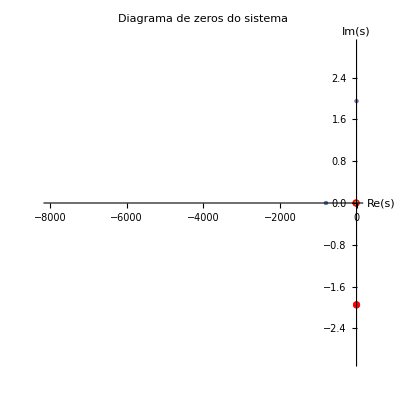

```mathematica
z = Solve[{Subscript[N, 1], Subscript[N, 2]} == 0, s];
Grid[{
  {"Zeros:", z//TableForm}
}]
ComplexListPlot[Values[z], 
    PlotRange -> {{-8000, 0}, {-3, 3}}, 
    AspectRatio -> 1,
    PlotStyle -> {PointSize[Large], Red},
    AxesLabel -> {"Re(s)", "Im(s)"},
    PlotLabel -> "Diagrama de zeros do sistema"]
```

Polos: | s→-929.118
s→-798.491
s→-12.8906
s→-5.39473
s→-2.91206-29.2524 ⅈ
s→-2.91206+29.2524 ⅈ
s→-0.220087-1.94957 ⅈ
s→-0.220087+1.94957 ⅈ

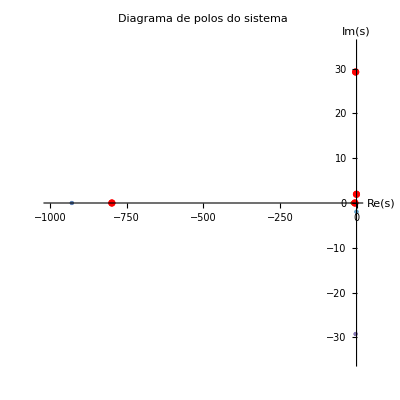

```mathematica
p = Solve[Subscript[D, s] == 0, s];
Grid[{
  {"Polos:", p//TableForm}
}]
ComplexListPlot[Values[p], 
    PlotRange -> {{-1000, 0}, {-35, 35}}, 
    AspectRatio -> 1,
    PlotStyle -> {PointSize[Large], Red},
    AxesLabel -> {"Re(s)", "Im(s)"},
    PlotLabel -> "Diagrama de polos do sistema"]
```

## Resposta em frequência